```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @Import["test1a.dat"];
nn=Length[l];
```

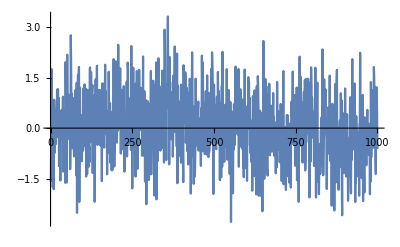

```mathematica
ListLinePlot[Take[l,UpTo[1000]]]
```

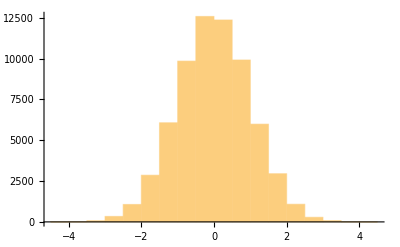

-6.71053×10^-9

1.00001

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.124295},{2,0.131572},{3,0.128529},{4,0.12817},{5,0.124156},{6,0.123097},{7,0.132131},{8,0.125818},{9,0.129115},{10,0.127358},{11,0.124669},{12,0.125299},{13,0.128923},{14,0.125634},{15,0.127987},{16,0.127034},{17,0.126642},{18,0.127468},{19,0.122981},{20,0.128115},{21,0.125008},{22,0.125943},{23,0.115696},{24,0.118157},{25,0.124995},{26,0.118056},{27,0.118006},{28,0.123584},{29,0.120041},{30,0.124128},{31,0.123148},{32,0.121685},{33,0.118927},{34,0.122185},{35,0.119812},{36,0.118109},{37,0.118977},{38,0.122746},{39,0.118559},{40,0.125137},{41,0.117202},{42,0.119658},{43,0.120708},{44,0.124244},{45,0.119027},{46,0.114797},{47,0.121202},{48,0.117782},{49,0.111882},{50,0.11573},{51,0.118726},{52,0.115529},{53,0.113462},{54,0.117716},{55,0.110683},{56,0.111393},{57,0.114175},{58,0.113832},{59,0.11398},{60,0.111636},{61,0.112658},{62,0.110637},{63,0.113389},{64,0.109234},{65,0.112334},{66,0.111447},{67,0.11184},{68,0.112151},{69,0.109136},{70,0.1146},{71,0.112602},{72,0.106079},{73,0.111383},{74,0.109066},{75,0.105929},{76,0.111363},{77,0.0986229},{78,0.105138},{79,0.10882},{80,0.106834},{81,0.108896},{82,0.107901},{83,0.103115},{84,0.108381},{85,0.108018},{86,0.107192},{87,0.102985},{88,0.103558},{89,0.105367},{90,0.105974},{91,0.109343},{92,0.105263},{93,0.0999067},{94,0.102755},{95,0.102342},{96,0.0978087},{97,0.104431},{98,0.100392},{99,0.0992129},{100,0.105515}}

{a→0.143487,b→0.00764799}

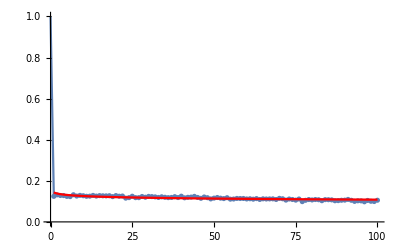

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

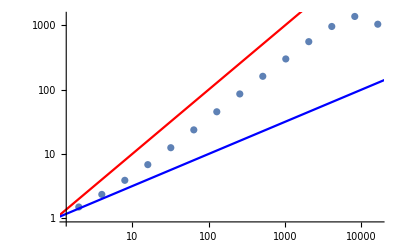

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1),x^(1/2)},{x,1,Length[l]},PlotStyle->{Red,Blue}];
Show[p1,p2]
```

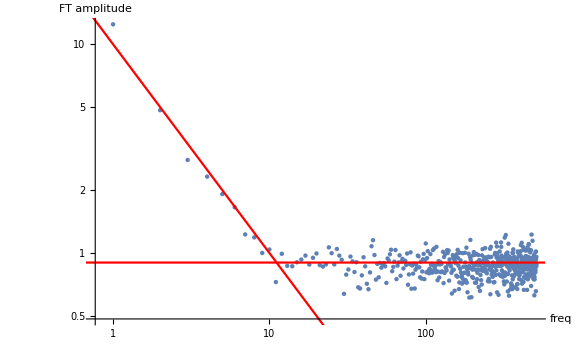

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"freq","FT amplitude"},LabelStyle->Larger];
pft2=LogLogPlot[{10/ω,0.9},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```